Author: Richard Brito

This notebook can be used to compute the gravitational-wave energy flux emitted by a scalar cloud around a black hole. It was mostly written to produce the results of Ref.[1] and [2]. Note that this has mostly been tested for the fastest-growing scalar mode l=m=1,n=0, but can in principle be used  for other l=m unstable modes.

Refs:
[1] Richard Brito, Shrobana Ghosh, Enrico Barausse, Emanuele Berti, Vitor Cardoso, Irina Dvorkin, Antoine Klein, Paolo Pani
,“Gravitational wave searches for ultralight bosons with LIGO and LISA” https://arxiv.org/abs/1706.06311
[2] Richard Brito, Shrobana Ghosh, Enrico Barausse, Emanuele Berti, Vitor Cardoso, Irina Dvorkin, Antoine Klein, Paolo Pani
,”Stochastic and resolvable gravitational waves from ultralight bosons
” https://arxiv.org/abs/1706.05097

## Gravitational radiation - Preliminaries [This generates auxiliary files needed for the computation. No need to run this if auxiliary files already available]

```mathematica
Quit[]
```

Define Kerr metric

```mathematica
x={t,r,θ,φ};

Δ=r^2+a^2-2M r;
Σ=r^2+a^2 Cos[θ]^2;
gdd={{-Δ/Σ+(a^2 Sin[θ]^2)/Σ,0,0,a Sin[θ]^2 Δ/Σ-Sin[θ]^2(a(r^2+a^2))/Σ},{0,Σ/Δ,0,0},{0,0,Σ,0},{a Sin[θ]^2 Δ/Σ-Sin[θ]^2(a(r^2+a^2))/Σ,0,0,-Δ a^2 Sin[θ]^4/Σ+Sin[θ]^2((r^2+a^2)^2)/Σ}};
(****)
guu=Simplify[Inverse[gdd]];
DET=Simplify[Det[gdd]];
dim=Length[gdd];
Do[g[i,j]=Simplify[gdd[[i]][[j]]];,{i,1,dim},{j,1,dim}];
```

Define tetrad

```mathematica
ln={(r^2+a^2)/(r^2-2M r +a^2),1,0,a/(r^2-2M r+a^2)};nn=1/(2(r^2+a^2 Cos[θ]^2)){r^2+a^2,-(r^2-2M r+a^2),0,a};mn=1/(√2(r+I a Cos[θ])){I a Sin[θ],0,1,I/Sin[θ]};mc=1/(√2(r-I a Cos[θ])){-I a Sin[θ],0,1,-I/Sin[θ]};
lnd=Table[Sum[ln[[i]]gdd[[i,j]],{i,1,dim}],{j,1,dim}]//Simplify;
nnd=Table[Sum[nn[[i]]gdd[[i,j]],{i,1,dim}],{j,1,dim}]//Simplify;
mnd=Table[Sum[mn[[i]]gdd[[i,j]],{i,1,dim}],{j,1,dim}]//Simplify;
mcd=Table[Sum[mc[[i]]gdd[[i,j]],{i,1,dim}],{j,1,dim}]//Simplify;
```

Check that tetrad is correct, by checking that we can can construct the metric from the tetrads.

```mathematica
Do[guu2[i,j]=-nn[[j]]ln[[i]]-nn[[i]]ln[[j]]+mn[[i]]mc[[j]]+mn[[j]]mc[[i]];,{i,1,4},{j,1,4}]//Simplify
Do[gdd2[i,j]=-nnd[[j]]lnd[[i]]-nnd[[i]]lnd[[j]]+mnd[[i]]mcd[[j]]+mnd[[j]]mcd[[i]];,{i,1,4},{j,1,4}]//Simplify
guu20=Table[guu2[i,j],{i,1,4},{j,1,4}]//FullSimplify;
guu==guu20//Simplify
gdd20=Table[gdd2[i,j],{i,1,4},{j,1,4}]//FullSimplify;
gdd==gdd20//Simplify
```

True

True

Scalar field' s stress - energy tensor : we use eq . 14 in  https://arxiv.org/pdf/1312.2326.pdf to write down the stress - energy tensor for the real scalar field [defined by Re(ϕ)] as T[Re(ϕ),Re(ϕ)]=(T(ϕ,ϕ)+T(ϕc,ϕc)+2T(ϕ,ϕc))/4 where ϕc is the complex conjugate of ϕ..

```mathematica
ϕ:=A0 R[r]S[θ] E^(I m φ)E^(-I ω t);
Do[TScal[i,j]=Simplify[(D[ϕ,x[[i]]]D[ϕ,x[[j]]])-1/2 g[i,j](Sum[guu[[l]][[p]]D[ϕ,x[[l]]]D[ϕ,x[[p]]],{l,1,dim},{p,1,dim}]+μ^2 ϕ ϕ)];,{i,1,dim},{j,1,dim}];
ϕc:=A0c Rc[r]S[θ] E^(-I m φ)E^(I ω t);
Do[TScalc[i,j]=Simplify[(D[ϕc,x[[i]]]D[ϕc,x[[j]]])-1/2 g[i,j](Sum[guu[[l]][[p]]D[ϕc,x[[l]]]D[ϕc,x[[p]]],{l,1,dim},{p,1,dim}]+μ^2 ϕc ϕc)];,{i,1,dim},{j,1,dim}];
Do[TScalabs[i,j]=Simplify[(D[ϕ,x[[i]]]D[ϕc,x[[j]]])-1/2 g[i,j](Sum[guu[[l]][[p]]D[ϕc,x[[l]]]D[ϕ,x[[p]]],{l,1,dim},{p,1,dim}]+μ^2 ϕc ϕ)];,{i,1,dim},{j,1,dim}];
```

Note that the terms T(ϕ,ϕ) and T(ϕc,ϕc) do not contribute to the total mass of the system because their integral vanishes when integrating the density over the azimuthal angle φ, so we do not add those terms  to the expression for the density ρdens.

```mathematica
ρdens=-1/4(2Sum[TScalabs[1,k]guu[[1,k]],{k,1,dim}]);
```

We here use the fact that the term T(ϕ,ϕc) is static so does not generate GWs whereas T(ϕ,ϕ) and T(ϕc,ϕc) generate GWs with mgw=+2m, ωgw=+2ω and mgw=-2m, ωgw=-2ω, respectively. The invariance of Teukolsky's equations under complex conjugation and ω→-ω, m→-m, allows to show that those two terms contribute the same to the GW power. So only need to consider the T(ϕ,ϕ) and then double the results at the end.

```mathematica
Do[TScalTotal[i,j]=Simplify[1/4(TScal[i,j])];,{i,1,dim},{j,1,dim}];
```

Below we use expressions from Sasaki & Tagoshi "Analytic Black Hole Perturbation Approach to Gravitational Radiation", Living Reviews. See https://arxiv.org/pdf/gr-qc/0306120.pdf, eq. 13. Note that we using a different normalization for the spheroidal harmonic than Sasaki & Tagoshi . We normalize the spheroidal harmonics such that ∫_s |S_lm|^2dΩ=1. See e.g. https://arxiv.org/pdf/1906.11257.pdf (eq. 55, note that T4=B2+B2star). Also note that integration over t and φ is already being done since it can be done analytically, and essentially selects the gravitational azimuthal number to be mgw=+2m, ωgw=+2ω and mgw=-2m, ωgw=-2ω. Also note that that m and ω appearing below are the scalar field’s azimuthal number and frequency, not the gravitational wave ones.

```mathematica
Jplus[Y_]:=D[Y,r]-1/(r^2-2M r+a^2)((r^2+a^2)(-2I ω)+a(2I m))Y;
Ls[Y_,s_]:=D[Y,θ]-I/Sin[θ](2I m)Y-I a Sin[θ](-2I ω)Y+s Cot[θ]Y;

ρ=1/(r-I a Cos[θ]);ρc=1/(r+I a Cos[θ]);

B2=-1/2 ρ^8 ρc Ls[ρ^-4 Ls[ρ^-2 ρc^-1 Tnn[r,θ],0],-1]-1/(2 √2)ρ^8 ρc(r^2-2M r+a^2)^2 Ls[ρ^-4 ρc^2 Jplus[ρ^-2 ρc^-2(r^2-2M r+a^2)^-1 Tnm[r,θ]],-1];
B2star=-1/4 ρ^8 ρc (r^2-2M r+a^2)^2 Jplus[ρ^-4 Jplus[ρ^-2 ρc Tmm[r,θ]]]-1/(2 √2)ρ^8 ρc(r^2-2M r+a^2)^2 Jplus[ρ^-4 ρc^2(r^2-2M r+a^2)^-1 Ls[ρ^-2 ρc^-2 Tnm[r,θ],-1]];
T=16 π^2 ρ^-4(r^2+a^2 Cos[θ]^2)(B2+B2star);
```

We note that we could have ignored terms proportional to g_μν in the stress-energy tensor when computing Tnn,Tnm and Tmm, since g_μν n^μ n^ν=0,etc..., so those terms do not contribute to the GW radiation.

```mathematica
Tnn[r_,θ_]=Sum[TScalTotal[i,j]nn[[i]]nn[[j]],{i,1,dim},{j,1,dim}]//Simplify;
Tnm[r_,θ_]=Sum[TScalTotal[i,j]mc[[i]]nn[[j]],{i,1,dim},{j,1,dim}]//Simplify;
Tmm[r_,θ_]=Sum[TScalTotal[i,j]mc[[i]]mc[[j]],{i,1,dim},{j,1,dim}]//Simplify;
```

```mathematica
SetDirectory[NotebookDirectory[]];
Put[{T},"auxiliary_files/Tfinal.m"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Put[{ρdens},"auxiliary_files/density.m"]
```

## Equations and Series expansions for s=-2 [This generates auxiliary files needed for the computation. No need to run this if auxiliary files already available. “Series Horizon” is only needed if we numerically integrate Teukolsky’s equation, not for the MST method]

#### Wave equation

```mathematica
$Assumptions={M>0,a>0};
rplus=M+√(M^2-a^2);
rminus=M-√(M^2-a^2);
Ωh=a/(rplus^2+a^2);
f[r_]:=Δ[r]/(r^2+a^2);
Δ[r_]:=r^2-2M r+a^2
```

```mathematica
V=(KK^2-2I s(r-M)KK)/Δ[r]+4I s ω r-λ;
KK=(r^2+a^2)ω-a m;
eqn=Δ[r]^-s D[Δ[r]^(s+1)D[R[r],r],r]+V R[r]//Simplify;
```

#### Series Horizon (this can take some time)

Here we do the standard series expansion at the horizon. The order of the expansion, ORDH, can be set freely. The higher ORDH the more accurate is the computation, but it can be extremely slow to compute all terms in the series expansion for very high ORDH

```mathematica
R[r_]:=(r-rplus)^AA(r-rplus)^-s(r-rminus)^-s h[r];
eqn1=eqn/(r-rplus)^AA(r-rplus)^s(r-rminus)^s//Simplify;
Clear[R]
```

```mathematica
ORDH=3;
h[r_]:=Sum[hh[i] (r-rplus)^i,{i,0,ORDH}]; 
ruleH={AA->(ⅈ (a m-2 M (M+√(-a^2+M^2)) ω))/(2 √(-a^2+M^2))};
ss=Series[eqn1//.ruleH,{r,rplus,ORDH}]//Simplify;
eqsH=Table[SeriesCoefficient[ss,i]==0,{i,1,ORDH}];
yh=Table[hh[i],{i,1,ORDH}];
Length[eqsH]
Length[yh]
seriesH0=Solve[eqsH,yh][[1]]//Simplify;
seriesH=Union[seriesH0,ruleH];
Clear[h]
```

#### Series Infinity (this can take some time)

Here we do the standard series expansion at infinity. Again the order is arbitrary, but a high number of terms is needed for s=-2 to achieve numerical stability.

```mathematica
R[r_]:=Exp[kk r] r^AA H[r];
eq1b=eqn/(ⅇ^(kk  r)r^AA)//Simplify;
Clear[R]
```

```mathematica
ORDINF=7;
H[r_]:=Sum[hhinf[i] r^-i,{i,0,ORDINF+10}];
ruleINF={kk^2->-ω^2,kk^4->ω^4,kk^6->-ω^6,AA->-(kk+kk s+ⅈ s ω+2 M ω^2)/kk};
ss1=Series[{eq1b}//.ruleINF,{r,∞,ORDINF}]//Chop;

eqs1=Table[SeriesCoefficient[ss1[[1]],i]==0,{i,-2,ORDINF}];
yinf=Table[hhinf[i],{i,1,ORDINF+1}];
systINF1=Solve[eqs1,yinf][[1]]//Simplify;
Clear[H,R]
```

This is needed to extract the coefficients of the asymptotic expansion at infinity with enough precision.

```mathematica
Qinf=((ⅇ^(kk  r)r^(-(kk+kk s+ⅈ s ω+2 M ω^2)/kk)Sum[hhinf[i]/r^i,{i,0,ORDINF+1}])//.Union[systINF1,{hhinf[0]->BB1,kk-> -I ω}])+ ((ⅇ^(kk  r)r^(-(kk+kk s+ⅈ s ω+2 M ω^2)/kk)Sum[hhinf[i]/r^i,{i,0,ORDINF+1}])//.Union[systINF1,{hhinf[0]->CC1,kk->I ω}]);
Qpinf=D[Qinf,r];

solBC=Solve[{(Qinf/.r->INF1)==Y1,(Qpinf/.r->INF1)==Y1p},{BB1,CC1}][[1]];
```

We store the equations to save time in future :

```mathematica
SetDirectory[NotebookDirectory[]];
Put[{systINF1,ORDINF,seriesH,ORDH,eqn,solBC},"auxiliary_files/series_GW.m"]
```

## Gravitational Radiation - Computation [after the auxiliary files have been created, only this part needs to be run. The auxiliary files are already available in https://github.com/richbrito/gw_superradiance, so if you cloned the whole repository you do not need to re-create them. ]

#### Load equations, source, density, etc...

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
$HistoryLength=0;
ext=Get["auxiliary_files/series_GW.m"];
extT=Get["auxiliary_files/Tfinal.m"];
extρ=Get["auxiliary_files/density.m"];

systINF1=ext[[1]];
ORDINF=ext[[2]];
seriesH=ext[[3]];
ORDH=ext[[4]];
eqn=ext[[5]]/.R->R2;
solBC=ext[[6]];

(*to avoid confusion between gravitational and scalar variables I change the naming of the scalar variable*)
T[r,θ]=extT[[1]]/.m->mS/.t->0/.φ->0/.ω->ωRS/.R->R0;
ρ[r,θ]=extρ[[1]]/.m->mS/.ω->ωRS/.R->R0/.Rc->Rc0;

(*scalar spheroidal harmonic for l=m . Since k=√(μ^2-ω^2)<<1 for all parameter space of interest we use an analytical expansion in k to compute the scalar field's angular function. Expression is valid up to O(a^5 k^5). TO DO: add possibility to compute this numerically and have l neq m?*)
S[θ_]:=Sin[θ]^l(1+(a^2 k^2 a2+a^4 k^4 a24) Cos[θ]^2+a^4 k^4 a4 Cos[θ]^4)/.a2->-1/(6+4 l)/.a24->(1+l)/((3+2 l)^3 (5+2 l))/.a4->1/(120+128 l+32 l^2)/.k->√(μ^2-ωRS^2)/.l->lS; 

$Assumptions={M>0,a> 0,r>0,a<M,ω>0};
Δ[r_]:=r^2+a^2-2 M r;
rplus=M+√(M^2-a^2);
rminus=M-√(M^2-a^2);
Ωh=a/(rplus^2+a^2);
f[r_]:=Δ[r]/(r^2+a^2);

(*Without loss of generality we use units in which G=c=M=1 for simplicity. M can be easily restored at the end.*)
M=1;
```

#### Scalar Eigenvalues and Eigenvectors using Leaver’s method

This function is used to compute the scalar field eigenvalues and eigenfunctions. Mostly follows Appendix A in https://arxiv.org/pdf/1312.2326.pdf.

```mathematica
EIGENS[a0_,μ0_,l0_,m0_,Rmax_,NITMAX_]:=(
paramS={l->l0,m-> m0,a-> a0,μ-> μ0};

(*Scalar Eigenvalue: Ref:arXiv:gr-qc/0511111v4*)
η1=m1;α1=η1;β1=η1;
h[l1_]:=Limit[((l1^2-1/4(α1+β1)^2)(l1^2-1/4(α1-β1)^2)(l1^2))/(2(l1-1/2)l1^3(l1+1/2)),m1->m];
f0=l(l+1);
f1=0;
f2=Limit[h[l1+1]-h[l1]-1,l1->l];

f3=0;
f4=Limit[-((l1+2) (h[l1+1]) (h[l1+2]))/(2(l1+1)(2l1+3))+(h[l1+1])^2/(2(l1+1))+((h[l1]) (h[l1+1]))/(2 l1^2+2l1)-(h[l1])^2/(2l1)+((l1-1) (h[l1-1]) (h[l1]))/(4 l1^2-2l1),l1->l];
Alms=f0+f1 a √(ω^2-μ^2)+ f2 (a √(ω^2-μ^2))^2+f3* (a √(ω^2-μ^2))^3+f4*(a √(ω^2-μ^2))^4//.paramS;

b=√(1-a^2);
q=-√(μ^2-ω^2);c0=1-2I ω-(2I)/b(ω-(a m)/2);c1=-4+4I(ω-I q(1+b))+(4I)/b(ω-(a m)/2)-2(ω^2+q^2)/q;c2=3-2I ω-(2I)/b(ω-(a m)/2)-2(q^2-ω^2)/q;c3=(2I(ω-I q)^3)/q+2(ω-I*q)^2*b+q^2*a^2+2*I*q*a*m-Alms-1-(ω-I*q)^2/q+2*q*b+(2*I)/b*((ω-I*q)^2/q+1)*(ω-(a*m)/2);c4=(ω-I*q)^4/q^2+2*I*ω*(ω-I*q)^2/q-(2*I)/b*(ω-I*q)^2/q*(ω-(a*m)/2);

γs=Function[n,n^2+(c2-3)*n+c4];
βs=Function[n,-2*n^2+(c1+2)*n+c3];αs=Function[n,n^2+(c0+1)*n+c0];
Leaver31[ω_?NumericQ]:=Module[{Rn},For[{n=NITMAX+100;Rn=-1.0;},n>0,{Rn=γs[n]/(βs[n]-αs[n]*Rn);n--;}
];Rn];

Leaver33[ω_?NumericQ]:=βs[0]/αs[0]-Leaver31[ω]/.paramS;

ωana=μ*√(1-(μ M)^2/(l+n0+1)^2)+I/24 ((a m)/M-2μ (M+√(M^2-a^2)))(M μ)^9/.n0->0/.paramS;
ωang=FindRoot[Leaver33[ω]==0,{ω,ωana}];


Nmax=Rmax;
ae[0]=1;
Ωh0=a/(rplus0^2+a^2);
rplus0=M+√(M^2-a^2);
rminus0=M-√(M^2-a^2);
ωc=m*Ωh0;
σ=(2*rplus0*(ω-ωc))/(rplus0-rminus0);
χ=(μ^2-2*ω^2)/q;
λ0=Alms+a^2 ω^2-2a m ω//.ω->ωang[[1]][[2]]/.paramS;

ae[1]=-βs[0]/αs[0]/.ω->ωang[[1]][[2]]/.paramS;

ii=1;
While[ii<Nmax,ae[ii+1]=-(βs[ii]*ae[ii]+γs[ii]*ae[ii-1])/αs[ii]/.ω->ωang[[1]][[2]]/.paramS
;ii=ii+1];

Rn0=E^(q r)(r-rplus0)^(-I σ)*(r-rminus0)^(I σ+χ-1)*Sum[ae[i]*((r-rplus0)/(r-rminus0))^i,{i,0,Nmax-1}]/.ω->ωang[[1]][[2]]/.paramS;
dRn0=D[Rn0,r];
ddRn0=D[dRn0,r];
Rnc0=E^(Conjugate[q ]r)(r-rplus0)^Conjugate[-I σ]*(r-rminus0)^Conjugate[I σ+χ-1]*Sum[Conjugate[ae[i]]*((r-rplus0)/(r-rminus0))^i,{i,0,Nmax-1}]/.ω->ωang[[1]][[2]]/.paramS;
dRnc0=D[Rnc0,r];
ddRnc0=D[dRnc0,r];


{ωang[[1]][[2]]}
)
```

#### GW flux computation using MST method. Here we use the MST method as implemented in the Black Hole Perturbation Toolkit: https://bhptoolkit.org. This method is recommended for better accuracy.

This function compute the GW flux dE/dt and amplitudes A_lm. These two quantities are related by  dE/dt=1/(2π)1/(M ωgw)(Mc/M)^2(Abs(A))^2 (this definition already takes into account the fact that positive and negative m modes contribute the same to the GW flux). Here ωgw is the GW angular frequency defined by ωgw=2 Re(ωS), where ωS is the scalar field’s frequency eigenvalue. These quantities can be used to compute the GW waveform using eqs. 26 and 28 in https://arxiv.org/pdf/1810.03812.pdf. 

The output of the function INTBHPT is a vector with entries {A_lm, ωS,  dE/dt} and the inputs are

μ0 -> coupling constant M*μ (note that we are using M=1, and units G=c=1)
a0 -> dimensionless BH spin
l0 -> GW angular number lgw
m0 -> GW azimuthal number mgw
EPSG  -> To avoid coordinate singularities at the BH horizon for numerical purposes the integration starts at rh*(1+EPSG). This must sufficiently small to avoid large numerical errors, but also not too small to avoid singularities.
INF0  -> Upper limit for the integration defined as 3*INF0. This must be sufficiently large to avoid large numerical errors.
Rmax  -> This defines the maximum coefficient in the series expansion that defines the scalar field solution (see eq. A8 in https://arxiv.org/pdf/1312.2326.pdf)
NITMAX  -> This defines the maximum coefficient in the recurrence relation used to compute s=-2 eigenvalue and corresponding spheroidal harmonic.
NITMAXS  -> This defines the maximum coefficient in the recurrence relation used to compute the scalar field eigenvalue ωS.

```mathematica
<<Teukolsky` (*before running make sure you have the Teukolsky package from the BHPT installed: https://bhptoolkit.org/Teukolsky/*)
$MinPrecision=60;
INTBHPT[μ0_,a0_,l0_,m0_,EPSG_,INF0_,Rmax_,NITMAX_,NITMAXS_]:=(
(*Note that I'm doing computations for scalar mode with l=m=1. For different modes please change lS0 and mS0. Current code only supports l=m*)

lS0=1;mS0=1;
scalar=EIGENS[a0,μ0,lS0,lS0,Rmax,NITMAXS];
ωR=SetPrecision[Re[scalar[[1]]],60];
A0=1;
A0c=1;

param={lS->lS0,mS->mS0,ω->2Sign[m0]Re[ωR],ωRS->ωR,l->l0,m-> m0,a-> a0,μ-> μ0,hh[0]->1,kk->k0n,k0->k0n};

k0n=I ω;
s=-2;
rplus=M+√(M^2-a^2);
rh=rplus//.param;
rhn=rh(1+EPSG);
INF=Abs[INF0];

(*Normalize scalar field's amplitude such total mass in the cloud Ea=1*)
density=ParametricNDSolveValue[{y'[θ]==2π(ρ[r,θ] (r^2+a^2 Cos[θ]^2) Sin[θ]//.param//.{R0[r]->Rn0,R0'[r]->dRn0,Rc0[r]->Rnc0,Rc0'[r]->dRnc0}),y[10^-20]==0},y,{θ,10^-20,π},{r}];
ρ0[r_]:=Re[density[r][π]];

 soldens=y/.NDSolve[{y'[r]==(ρ0[r]),y[INF*3]==0},y,{r,rhn,INF*3}][[1]];
Ea=soldens[3INF]-soldens[rhn];

A02=A01/.NSolve[A01^2(Ea)==1,A01][[2]];

(*calculating the eigenvalues Subscript[A, lms]*)
km=1/2*Abs[m-s];kp=1/2*Abs[m+s];Alm=l*(l+1)-s*(s+1)-(2m s^2)/(l(l+1))a ω//.param;
γ=Function[n,2*a*ω*(n+km+kp+s)//.param];
β=Function[n,n*(n-1)+2*n*(km+kp+1-2*a*ω)-(2*a*ω*(2*km+s+1)-(km+kp)*(km+kp+1))-(a^2*ω^2+s*(s+1)+Sep)//.param];
α=Function[n,-2*(n+1)*(n+2*km+1)//.param];
Leaver31ang[Sep_]:=Module[{Rp},
For[{n=NITMAX;Rp=0;},n>0,{Rp=γ[n]/(β[n]-α[n]*Rp);n--;}
];Rp];
Leaver33ang[Sep_]:=β[0]/α[0]-Leaver31ang[Sep];

A=FindRoot[Leaver33ang[Sep]==0,{Sep,Alm}][[1,2]];

λ=A+a^2 ω^2-2a m ω//.param;


(*get IN solutions i.e. solution with ingoing BCs at the horizon*)

R=TeukolskyRadial[s,l0,m0,a0,ω//.param];
Rn=R["In"][r];
Rnp=R["In"]'[r];

(*Wronskian*)
W=(R["In"][r0]R["Up"]'[r0]-R["Up"][r0]R["In"]'[r0])(r0^2-2M r0+a^2)^(s+1)//.param/.r0->30;

(*match with asymptotic solution to get full solution up to r->infinity*)
rjunc=40;
CCn=CC1//.Union[solBC,param,{r->rjunc,INF1->rjunc,Y1-> Rn,Y1p-> Rnp,kk-> k0n}];
BBn=BB1//.Union[solBC,param,{r-> rjunc,INF1->rjunc,Y1-> Rn,Y1p-> Rnp,kk->-k0n}];

OUT=CCn;IN=BBn;

Qinf=((ⅇ^(kk  r)r^(-(kk+kk s+ⅈ s ω+2 M ω^2)/kk)Sum[hhinf[i]/r^i,{i,0,ORDINF+1}])//.Union[systINF1,{hhinf[0]->BB1,kk-> -I ω}])+ ((ⅇ^(kk  r)r^(-(kk+kk s+ⅈ s ω+2 M ω^2)/kk)Sum[hhinf[i]/r^i,{i,0,ORDINF+1}])//.Union[systINF1,{hhinf[0]->CC1,kk->I ω}]);

Rdata=Table[{r,R["In"][r]},{r,rhn,rjunc,0.1`60}];
Rint=Interpolation[Rdata];

Rh[r_]:=Piecewise[{{Rint[r],rhn≤ r< rjunc-1},{Qinf/.param/.BB1->IN/.CC1->OUT, r≥rjunc-1}}];


(*Spheroidal harmonic*)
ar=a//.param;
br=Sqrt[1-4*ar^2];rminus=(1-br)/2;rplus=(1+br)/2;
k1=1/2*Abs[m-s]//.param;
k2=1/2*Abs[m+s]//.param;
wang=ω//.param;
Sep=A;
w=wang;

γang=Function[n,2*ar*wang*(n+k1+k2+s)];βang=Function[n,n*(n-1)+2*n*(k1+k2+1-2*ar*wang)-(2*ar*wang*(2*k1+s+1)-(k1+k2)*(k1+k2+1))-(ar^2*wang^2+s*(s+1)+Sep)];αang=Function[n,-2*(n+1)*(n+2*k1+1)];

Nmax=NITMAX;sima=(w*rplus-ar*m)/br//.param;ae[0]=1;ae[1]=-βang[0]/αang[0];i=1;While[i<Nmax,ae[i+1]=(-βang[i]*ae[i]-γang[i]*ae[i-1])/(αang[i]);i=i+1];Sang=Exp[ar*w*u]*(1+u)^(1/2*Abs[m-s])*(1-u)^(1/2*Abs[m+s])*Sum[ae[i]*(1+u)^(i),{i,0,Nmax-1}]//.param;Normalization=1/Sqrt[2π NIntegrate[Sang*Conjugate[Sang],{u,-1,1}(*,MaxRecursion->12,PrecisionGoal->16,AccuracyGoal->16*)]];SangNormal=Normalization*Sang/.u->Cos[θ];

(*Computing the source*)
source0=ParametricNDSolveValue[{y'[θ]==(T[r,θ] Sin[θ]Conjugate[SangNormal]//.param/.{R0[r]->Rn0,R0'[r]->dRn0,R0''[r]->ddRn0}/.r->ri),y[10^-20]==0},y,{θ,10^-20,π},{ri}];


S0[ri_]:=source0[ri][π];

sol1=y/.NDSolve[{y'[r]==(1/((r^2-2M r+a^2)^2)Rh[r]*S0[r]/.param),y[3*INF]==0},y,{r,rhn,3*INF}][[1]];

Aa=sol1[3*INF]-sol1[rhn];

(*computing flux*)
Rinf=A02^2/W*(Aa)//.param;

(*factor 2 to account for the m=-2*)
fluxinf=2 1/(4π ω^2)*Abs[Rinf]^2//.param;

{Rinf,scalar[[1]],fluxinf}
);
```

```mathematica
xx=0.25;
INTBHPT[xx,0.9`60,2,2,10^-4,40/xx^2,30,100,1000]
```

{4.19582×10^-6+1.13409×10^-7 ⅈ,0.247919+7.54434×10^-9 ⅈ,1.14049×10^-11}

#### GW flux computation by numerically integrating Teukolsky’s equation This method can be faster than the MST method at the expense of being less accurate. No need to run this if you use the MST method. This is based on the code that was used in https://arxiv.org/abs/1706.06311

See previous section for options.

```mathematica
INT[μ0_,a0_,l0_,m0_,EPSG_,INF0_,Rmax_,NITMAX_,NITMAXS_]:=(
(*Note that I'm doing computations for scalar mode with l=m=1. For different modes please change lS0 and mS0. Note that current code only supports l=m*)

lS0=1;mS0=1;

scalar=EIGENS[a0,μ0,lS0,mS0,Rmax,NITMAXS];
ωR=Re[scalar[[1]]];
A0=1;
A0c=1;

ruleP={AccuracyGoal->80,PrecisionGoal->12,MaxSteps->10^6,WorkingPrecision->20};
param={lS->lS0,mS->mS0,ω->2Sign[m0]Re[ωR],ωRS->ωR,l->l0,m-> m0,a-> a0,μ-> μ0,hh[0]->1,kk->k0n,k0->k0n};

k0n=I ω;
s=-2;
rplus=M+√(M^2-a^2);
rh=rplus//.param;
rhn=rh(1+EPSG);
rhnG=rh(1+EPSG);
INF=Abs[INF0];

(*Normalize scalar field's amplitude such total mass in the cloud Ea=1*)
density=ParametricNDSolveValue[{y'[θ]==2π(ρ[r,θ] (r^2+a^2 Cos[θ]^2) Sin[θ]//.param//.{R0[r]->Rn0,R0'[r]->dRn0,Rc0[r]->Rnc0,Rc0'[r]->dRnc0}),y[10^-20]==0},y,{θ,10^-20,π},{r}];
ρ0[r_]:=Re[density[r][π]];

 soldens=y/.NDSolve[{y'[r]==(ρ0[r]),y[INF*3]==0},y,{r,rhn,INF*3}][[1]];
Ea=soldens[3INF]-soldens[rhn];

A02=A01/.NSolve[A01^2(Ea)==1,A01][[2]];

(*calculating the eigenvalues Subscript[A, lms]*)
km=1/2*Abs[m-s];kp=1/2*Abs[m+s];Alm=l*(l+1)-s*(s+1)-(2m s^2)/(l(l+1))a ω//.param;
γ=Function[n,2*a*ω*(n+km+kp+s)//.param];
β=Function[n,n*(n-1)+2*n*(km+kp+1-2*a*ω)-(2*a*ω*(2*km+s+1)-(km+kp)*(km+kp+1))-(a^2*ω^2+s*(s+1)+Sep)//.param];
α=Function[n,-2*(n+1)*(n+2*km+1)//.param];
Leaver31ang[Sep_]:=Module[{Rp},
For[{n=NITMAX;Rp=0;},n>0,{Rp=γ[n]/(β[n]-α[n]*Rp);n--;}
];Rp];
Leaver33ang[Sep_]:=β[0]/α[0]-Leaver31ang[Sep];

A=FindRoot[Leaver33ang[Sep]==0,{Sep,Alm}][[1,2]];

λ=A+a^2 ω^2-2a m ω//.param;


(*Integrate starting at the BH horizon to get IN solution (i.e. solution with ingoing BCs at the horizon*)

Rg=(r-rplus)^((ⅈ (a m-2 M (M+√(-a^2+M^2)) ω))/(2 √(-a^2+M^2)))(r-rplus)^-s(r-rminus)^-s Sum[hh[i](r-rplus)^i,{i,0,ORDH}]//.Union[param,seriesH];
BCs={R2[rhnG]==Rg/.r->rhnG,R2'[rhnG]==D[Rg,r]/.r->rhnG}//.param;
EQs={eqn==0}//.param;
sol=NDSolve[Union[EQs,BCs],R2[r],{r,rhnG,2000},ruleP];
Rn=R2[r]/.sol[[1]];
Rnp=D[Rn,r];

(*match with asymptotic solution to get full solution up to r->infinity and to compute Wronskian*)
CCn=CC1//.Union[solBC,param,{r->300,INF1->300,Y1-> Rn,Y1p-> Rnp,kk-> k0n}];
BBn=BB1//.Union[solBC,param,{r-> 300,INF1->300,Y1-> Rn,Y1p-> Rnp,kk->-k0n}];

OUT=CCn;IN=BBn;


W=2*I*ω*IN//.param;

Qinf=((ⅇ^(kk  r)r^(-(kk+kk s+ⅈ s ω+2 M ω^2)/kk)Sum[hhinf[i]/r^i,{i,0,ORDINF+1}])//.Union[systINF1,{hhinf[0]->BB1,kk-> -I ω}])+ ((ⅇ^(kk  r)r^(-(kk+kk s+ⅈ s ω+2 M ω^2)/kk)Sum[hhinf[i]/r^i,{i,0,ORDINF+1}])//.Union[systINF1,{hhinf[0]->CC1,kk->I ω}]);


Rh[r_]:=Piecewise[{{Rg,rh≤ r<rhnG},{R2[r]/.sol[[1]],rhnG≤ r≤ 300},{Qinf/.param/.BB1->IN/.CC1->OUT, r>300}}];

(*Spheroidal harmonic*)
ar=a//.param;
br=Sqrt[1-4*ar^2];rminus=(1-br)/2;rplus=(1+br)/2;
k1=1/2*Abs[m-s]//.param;
k2=1/2*Abs[m+s]//.param;
wang=ω//.param;
Sep=A;
w=wang;

γang=Function[n,2*ar*wang*(n+k1+k2+s)];βang=Function[n,n*(n-1)+2*n*(k1+k2+1-2*ar*wang)-(2*ar*wang*(2*k1+s+1)-(k1+k2)*(k1+k2+1))-(ar^2*wang^2+s*(s+1)+Sep)];αang=Function[n,-2*(n+1)*(n+2*k1+1)];

Nmax=NITMAX;sima=(w*rplus-ar*m)/br//.param;ae[0]=1;ae[1]=-βang[0]/αang[0];i=1;While[i<Nmax,ae[i+1]=(-βang[i]*ae[i]-γang[i]*ae[i-1])/(αang[i]);i=i+1];Sang=Exp[ar*w*u]*(1+u)^(1/2*Abs[m-s])*(1-u)^(1/2*Abs[m+s])*Sum[ae[i]*(1+u)^(i),{i,0,Nmax-1}]//.param;Normalization=1/Sqrt[2π NIntegrate[Sang*Conjugate[Sang],{u,-1,1}(*,MaxRecursion->12,PrecisionGoal->16,AccuracyGoal->16*)]];SangNormal=Normalization*Sang/.u->Cos[θ];

(*Computing the source*)
source0=ParametricNDSolveValue[{y'[θ]==(T[r,θ] Sin[θ]Conjugate[SangNormal]//.param/.{R0[r]->Rn0,R0'[r]->dRn0,R0''[r]->ddRn0}/.r->ri),y[10^-20]==0},y,{θ,10^-20,π},{ri}];


S0[ri_]:=source0[ri][π];

 sol1=y/.NDSolve[{y'[r]==(1/((r^2-2M r+a^2)^2)Rh[r]S0[r]/.param),y[INF*3]==0},y,{r,rhn,INF*3}][[1]];

Aa=sol1[3INF]-sol1[rhn];

(*computing flux*)
Rinf=A02^2/W*(Aa)//.param;

(*factor 2 to account for the m=-2*)
fluxinf=2 1/(4π ω^2)*Abs[Rinf]^2//.param;

{Rinf,scalar[[1]],fluxinf}
);
```

```mathematica
xx=0.25;
INT[xx,0.9,2,2,10^-4,40/xx^2,50,100,1000]
```

NDSolve::precw: The precision of the differential equation ({{R2[1.43603]==-2.29463×10^-8-2.42678×10^-8 ⅈ,R2'[1.43603]==-0.000246776-0.000406927 ⅈ,(-1.07259-(0.+3.9667 ⅈ) r+Power[«2»] Plus[«2»] Plus[«3»]) R2[r]-2 (-1+r) R2'[r]+(0.81+Plus[«2»] r) R2''[r]==0},{},{},{},{}}) is less than WorkingPrecision (20.).

{3.29818×10^-6-2.84404×10^-6 ⅈ,0.247919+7.54434×10^-9 ⅈ,1.22781×10^-11}

#### Making files with GW amplitudes Use this to obtain A_lm vs Mμ (or dE/dt_lmvs Mμ) assuming that the BH is at the superradiant threshold χ=χc.

Here I assume that BH dimensionless spin is χ=χc=(4*m*M*ωR)/(m^2+4 M^2 ωR^2) , where ωR is the scalar field eigenvalue for a given α=Mμ.

```mathematica
ln=3;
mn=2;
(****)
μi=0.09;
μf=0.1;
dim=41;
dμ=(μf-μi)/dim;
(****)
(****)
TT={};
xx=μi;

Monitor[
For[j=1,j<dim+1,

(*Note that the scalar field eigenvalue ωS depends very weakly on the BH spin and ωS~μ (see e.g. Fig. 5 in https://arxiv.org/pdf/0705.2880.pdf), so when computing ωS I approximate the critical spin to be ~(4*m*M*μ)/(m^2+4 M^2 μ^2)*)
ωRI=EIGENS[(4*xx)/(1+4 xx^2),xx,1,1,50,300][[1]];

atn=SetPrecision[(4*Re[ωRI])/(1+4 Re[ωRI]^2)//N,60];

yn=INTBHPT[xx,atn,ln,mn,10^-5,50/xx^2,50,100,300];(*use INT instead of INTBHPT if using direct integration method*)


FREQR=Re[yn[[2]]];
FREQI=Im[yn[[2]]];
ZZ=yn[[1]];
FLUX=yn[[3]];

AppendTo[TT,{xx,ZZ//Abs(*,FLUX*)}];
j++;
xx=xx+dμ;
],{j,xx,atn,ZZ//Abs,FLUX,FREQR,FREQI}]
```

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["../Data/Z22_MST.dat",TT];*)
```

#### Plots

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*this data uses the "direct integration method" and is the data that was used in Fig.2 of https://arxiv.org/abs/1706.06311*)
Z22dir=Import["../Data/Z22_direct.dat"];
Z32dir=Import["../Data/Z32_direct.dat"];

(*this data used the MST method instead*)
Z22MST=Import["../Data/Z22_MST.dat"];
Z32MST=Import["../Data/Z32_MST.dat"];

(*this is data that was used for Fig. 2 in https://arxiv.org/abs/1706.06311 (obtained using a direct integration method to compute the homogeneous solutions to Teukolsky's equations*)
dE22dt=Import["../Data/fluxGWl2m2.dat"];
dE32dt=Import["../Data/fluxGWl3m2.dat"];
```

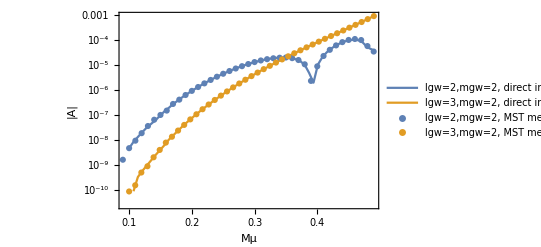

```mathematica
(*check that both MST and direct integration methods agree (within numerical error)*)
Show[ListLogPlot[{Z22dir,Z32dir},Joined->True,Frame->True,PlotLegends->{"lgw=2,mgw=2, direct integration","lgw=3,mgw=2, direct integration"},FrameLabel->{"Mμ","|A|"}],ListLogPlot[{ Z22MST,Z32MST},PlotLegends->{"lgw=2,mgw=2, MST method","lgw=3,mgw=2, MST method"}]]
```

```mathematica
(*the fit for the lgw=mgw=2 curve should be such that in the Mμ<<1 limit we recover the analytical estimate given by eq. 13 in https://arxiv.org/pdf/1411.0686.pdf*)
$Assumptions={α>0};
√(2π*(2α)^2(484+9 π^2)/23040 α^14)//N//Simplify
```

0.790479 α^8

```mathematica
(*These are the fits used in gwaxion v0.0.1 (https://github.com/maxisi/gwaxion/tree/v0.0.1)*)
nlm22=NonlinearModelFit[Z22dir,{0.7904787874157165 x^8+a  x^9+c x^10},{a,c},x]//Normal
nlm32=NonlinearModelFit[Z32dir,{a x^10+ c x^12,a>0},{a,c},x]//Normal
```

0.790479 x^8-2.94175 x^9+2.80312 x^10

1.08158 x^10-0.400642 x^12

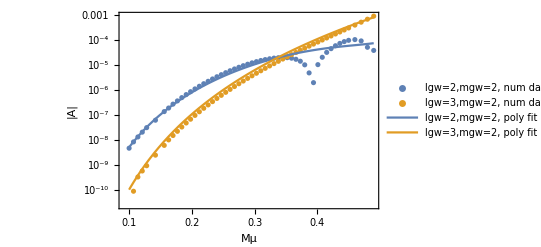

```mathematica
Show[ListLogPlot[{Z22dir,Z32dir},PlotStyle->Dashed,Frame->True,PlotLegends->{"lgw=2,mgw=2, num data","lgw=3,mgw=2, num data"},FrameLabel->{"Mμ","|A|"}],LogPlot[{ nlm22,nlm32},{x,0.1,0.49},PlotLegends->{"lgw=2,mgw=2, poly fit","lgw=3,mgw=2, poly fit"}]]
```

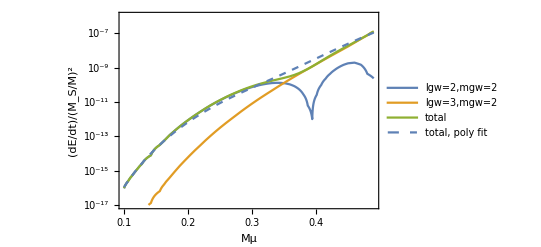

```mathematica
(*Plot with total flux. The "total" curve below is what is shown in Fig. 2 of https://arxiv.org/abs/1706.06311*)
dE22dtint=Interpolation[dE22dt,InterpolationOrder->1];
dE32dtint=Interpolation[dE32dt,InterpolationOrder->1];
dE22fit=1/(2π(2Mμ(1-Mμ^2/8))^2)nlm22^2/.x->Mμ;
dE32fit=1/(2π(2Mμ(1-Mμ^2/8))^2)nlm32^2/.x->Mμ;

Show[LogPlot[{dE22dtint[Mμ],dE32dtint[Mμ],dE22dtint[Mμ]+dE32dtint[Mμ]},{Mμ,0.1,0.49},Frame->True,PlotLegends->{"lgw=2,mgw=2","lgw=3,mgw=2","total"},FrameLabel->{"Mμ","(dE/dt)/(M_S/M)^2"},PlotRange->{{0.1,0.49},{10^-17,10^-6}}],
LogPlot[{dE22fit+dE32fit},{Mμ,0.1,0.49},PlotStyle->Dashed,PlotLegends->{"total, poly fit"}]]
```

```mathematica
(*check errors of the polynomial fits*)
error22=Table[{Z22dir[[i,1]],Abs[(nlm22/.x->Z22dir[[i,1]])/(Z22dir[[i,2]])-1]},{i,2,Length[Z22dir]}];
error32=Table[{Z32dir[[i,1]],Abs[(nlm32/.x->Z32dir[[i,1]])/(Z32dir[[i,2]])-1]},{i,2,Length[Z32dir]}];
```

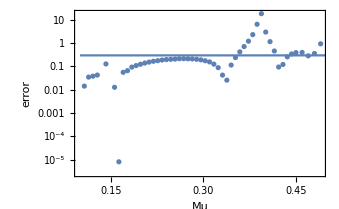

```mathematica
Show[ListLogPlot[{error22},Frame->True,FrameLabel->{"Mμ","error"}],LogPlot[0.3,{x,0.1,0.5}]]
```

#### Piecewise fit

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*this data used the MST method instead*)
Z22MST=Import["../Data/Z22_MST.dat"];
Z32MST=Import["../Data/Z32_MST.dat"];

dE22dt=Table[{Z22MST[[i,1]],Z22MST[[i,2]]^2/(2π(2Z22MST[[i,1]](1-Z22MST[[i,1]]^2/8))^2)},{i,1,Length[Z22MST]}];dE32dt=Table[{Z32MST[[i,1]],Z32MST[[i,2]]^2/(2π(2Z32MST[[i,1]](1-Z32MST[[i,1]]^2/8))^2)},{i,1,Length[Z32MST]}];

dE22dtdir=Import["../Data/fluxGWl2m2.dat"];
dE32dtdir=Import["../Data/fluxGWl3m2.dat"];
```

```mathematica
nlm22=NonlinearModelFit[Drop[Z22MST,-29],{0.7904787874157165 x^8+a  x^9+c x^10},{a,c},x]//Normal
nlm32=NonlinearModelFit[Z32MST,{a x^10+ c x^12+d x^14,a>0},{a,c,d},x]//Normal
```

0.790479 x^8-3.74249 x^9+8.01411 x^10

1.09563 x^10-6.93726 x^12+28.6718 x^14

```mathematica
sol=Solve[{(nlm22/.x->0.2)==(a x^0+ c x^1+d x^2+e x^3+f x^4/.x->0.2),(D[nlm22,x]/.x->0.2)==(D[a x^0+ c x^1+d x^2+e x^3+f x^4,x]/.x->0.2)},{a,c}][[1]]//Simplify;
fit=a x^0+ c x^1+d x^2+e x^3+f x^4/.sol//Simplify;
nlm22int=NonlinearModelFit[Drop[Drop[Z22MST,11],-15],{fit},{d,e,f},x]//Normal//Simplify
```

-0.00028437+0.0049161 x-0.0314712 x^2+0.0877599 x^3-0.0882204 x^4

```mathematica
solint2=Solve[{(nlm22int/.x->0.32)==(a x^0+ c x^1+d x^2+e x^3+f x^4/.x->0.32),(D[nlm22int,x]/.x->0.32)==(D[a x^0+ c x^1+d x^2+e x^3+f x^4,x]/.x->0.32)},{a,c}][[1]]//Simplify;
fitint2=a x^0+ c x^1+d x^2+e x^3+f x^4/.solint2//Simplify;
nlm22int2=NonlinearModelFit[Drop[Drop[Z22MST,23],-10],{fitint2},{d,e,f,g,h,w,z},x]//Normal//Simplify
```

-0.00219195+0.030448 x-0.158712 x^2+0.367869 x^3-0.318227 x^4

```mathematica
solend=Solve[{(nlm22int2/.x->0.39)==(a x^0+ c x^1+d x^2+e x^3+f x^4+g x^5+h x^6/.x->0.39),(D[nlm22int2,x]/.x->0.39)==(D[a x^0+ c x^1+d x^2+e x^3+f x^4+g x^5+h x^6,x]/.x->0.39)},{a,c}][[1]]//Simplify;
fitend=a x^0+ c x^1+d x^2+e x^3+f x^4+g x^5+h x^6/.solend//Simplify;
nlm22end=NonlinearModelFit[Drop[Z22MST,31],{fitend},{d,e,f,g,h,w,z},x]//Normal//Simplify
```

57.616-799.87 x+4621.28 x^2-14222.2 x^3+24588.7 x^4-22642.6 x^5+8675.74 x^6

```mathematica
nlm22all=Piecewise[{{nlm22,x≤ 0.2},{nlm22int,0.2<x≤0.32},{nlm22int2,0.32<x≤ 0.39},{nlm22end,0.39<x}}];
```

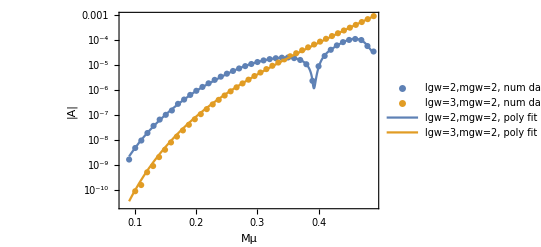

```mathematica
Show[ListLogPlot[{Z22MST,Z32MST},PlotStyle->Dashed,Frame->True,PlotLegends->{"lgw=2,mgw=2, num data","lgw=3,mgw=2, num data"},FrameLabel->{"Mμ","|A|"}],LogPlot[{ nlm22all,nlm32},{x,0.09,0.49},PlotLegends->{"lgw=2,mgw=2, poly fit","lgw=3,mgw=2, poly fit"}]]
```

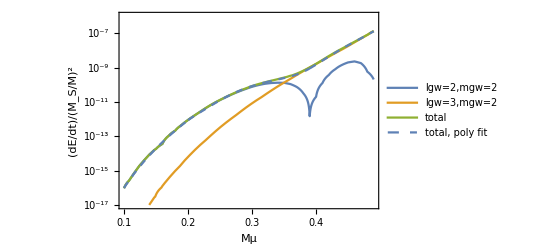

```mathematica
dE22dtint=Interpolation[dE22dt,InterpolationOrder->1];
dE32dtint=Interpolation[dE32dt,InterpolationOrder->1];
dE22dir=Interpolation[dE22dtdir,InterpolationOrder->1];
dE32dir=Interpolation[dE32dtdir,InterpolationOrder->1];
dE22fit=1/(2π(2Mμ(1-Mμ^2/8))^2)nlm22all^2/.x->Mμ;
dE32fit=1/(2π(2Mμ(1-Mμ^2/8))^2)nlm32^2/.x->Mμ;

Show[LogPlot[{dE22dtint[Mμ],dE32dtint[Mμ],dE22dtint[Mμ]+dE32dtint[Mμ]},{Mμ,0.1,0.49},Frame->True,PlotLegends->{"lgw=2,mgw=2","lgw=3,mgw=2","total"},FrameLabel->{"Mμ","(dE/dt)/(M_S/M)^2"},PlotRange->{{0.1,0.49},{10^-17,10^-6}}],
LogPlot[{dE22fit+dE32fit},{Mμ,0.1,0.49},PlotStyle->Dashed,PlotLegends->{"total, poly fit"}]]
```

```mathematica
error22=Table[{Z22MST[[i,1]],Abs[(nlm22all/.x->Z22MST[[i,1]])/(Z22MST[[i,2]])-1]},{i,2,Length[Z22MST]}];
error32=Table[{Z32MST[[i,1]],Abs[(nlm32/.x->Z32MST[[i,1]])/(Z32MST[[i,2]])-1]},{i,2,Length[Z32MST]}];
```

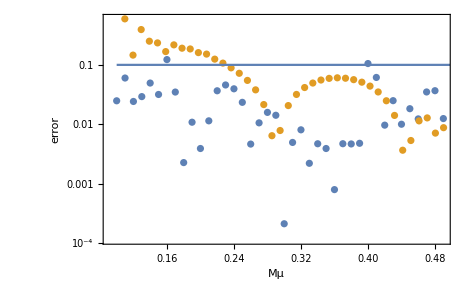

```mathematica
Show[ListLogPlot[{error22,error32},Frame->True,FrameLabel->{"Mμ","error"}],LogPlot[0.1,{x,0.1,0.5}]]
```

## Scalar angular function [This is just used to check that expression used for the scalar spheroidal harmonic is correct. No need to run this]

### Analytical expression for scalar spheroidal harmonic for l=m (valid up to O(a^5 k^5) with k=√(μ^2-ω^2) and a=J/M)

```mathematica
$Assumptions={l>0};
```

```mathematica
EQmass=1/Sin[θ] D[Sin[θ]D[S[θ],θ],θ]+(-a^2 k^2 Cos[θ]^2-m^2/Sin[θ]^2+Alm)S[θ];
```

```mathematica
S[θ_]:=Sin[θ]^l(1+(a^2 k^2 a2+a^4 k^4 a24) Cos[θ]^2+a^4 k^4 a4 Cos[θ]^4)/.a2->-1/(6+4 l)/.a24->(1+l)/((3+2 l)^3 (5+2 l))/.a4->1/(120+128 l+32 l^2);
```

```mathematica
(*check that angular equation is solved up to order O(a^5 k^5). We note that this is a very good approximation to the scalar spheroidal harmonic because k always satisfies k<<1 for bound states and a is at most unity*)
Series[EQmass,{a,0,4}]/.Alm->l(l+1)+(a^2 k^2)/(3+2l)-(2 a^4 k^4 (1+l))/((3+2 l)^3 (5+2 l))/.m->l//.Sin[θ]^2->1-Cos[θ]^2//FullSimplify
```

O[a]^5